## Naloga 1

Obravnavaj met žogice iz višine H v smeri vektorja v0 = {v0x, v0y}.Upoštevaj gravitacijski pospešek g = 9.81 m/s2.Pomagaj si z naslednjimi koraki :

```mathematica
v0={10,3};
GG=9.81;
H=10;
a ={0,-GG};
x0 ={0,H};
v[t_] := {v0 [[1]],v0[[2]] - GG*t}
v[t_] := v0 + a *t
v[1]
```

{10,-6.81}

```mathematica
X[t_] := x0 + v0 * t + (a * t^2)/2
X[1]
```

{10,8.095}

```mathematica
SlikaTocke[t_] :={PointSize[0.03],Point[X[t]]}

Manipulate[Graphics[SlikaTocke[t],Axes->True, PlotRange->{{0,20},{0,15}}, AspectRatio->Automatic],{t,0,1.766035}]
SlikaVektorja[t_] := {Arrowheads[0.05], Arrow[{X[t], X[t]+v[t]}]}
```

```mathematica
SlikaVektorja[t_] := {Arrowheads[0.05], Arrow[{X[t], X[t]+v[t]}]}

Manipulate[Graphics[{SlikaTocke[t] ,SlikaVektorja[t]},Axes->True, PlotRange->{{0,20},{0,15}}, AspectRatio->Automatic],{t,0,1.076}]
```

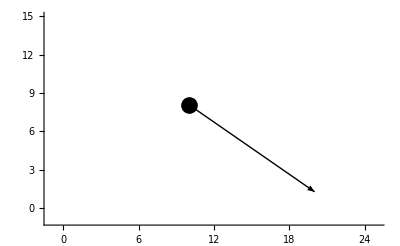

```mathematica
Graphics[{SlikaTocke[1] ,SlikaVektorja[1]},Axes->True, PlotRange->{{-1,25},{-1,15}}, AspectRatio->Automatic]
```

```mathematica
Manipulate[Graphics[{SlikaTocke[t] ,SlikaVektorja[t]},Axes->True, PlotRange->{{0,100},{-100,20}}, AspectRatio->Automatic],{t,0,5}]
```

```mathematica
Y[t_] := (H + v0 * t) - (GG * t^2)/2
SamoY[{x_,y_}] := y 
rez = Solve[SamoY[Y[t]]== 0,t];
rez = SamoY[rez]
Y[1.766035031964932]
```

{t→1.76604}

{12.3622,3.55271×10^-15}

```mathematica
Hitrost = √(v0[[1]]^2+v0[[2]]^2);
casLetaDoNajvišjeTočke = (2*Hitrost*sinkot)/(GG * 2)
sinkot =SamoY[v0]/Hitrost //N ;
MaksimalnaVišina = (Hitrost^2* sinkot^2)/(2*GG)+ H
```

1.06425 sinkot

10.4587

```mathematica
domet  =Hitrost^2 *Sin[2*ArcSin[sinkot]]/GG + H;
Manipulate[Graphics[{SlikaTocke[t],Arrow[{X[t], X[t]+v[t]}]}, Axes->True, PlotRange->{ {-1, domet +4},{-4, MaksimalnaVišina + 4}}, AspectRatio-> Automatic],{t, 0, casLeta}
]
```

```mathematica
casLeta= casLetaDoNajvišjeTočke + √((2*MaksimalnaVišina)/GG);
absHitrosti=√((v[casLeta][[1]])^2  + (v[casLeta][[2]])^2)
casLeta
```

17.47

1.76604

## Naloga 2

Ravnino podamo v obliki Ravnina[n_, v_], kjer je n normala na ravnino in je v točka na
ravnini.Npr.ravnina, ki gre skozi točko (1, 1, 1) in je pravokotna na glavno diagonalo je r111 = Ravnina[{-1, -1, -1}, {1, 1, 1}].

```mathematica
r111 = Ravnina[{-1,-1,-1},{1,1,1}]
Slika[Ravnina[n_,v_]] := Hyperplane[n,v]
```

Ravnina[{-1,-1,-1},{1,1,1}]

```mathematica
Format[r_Ravnina] := Graphics3D[Slika[r]]
```

```mathematica
Normala[Ravnina[n_,v_]] := n
Normala[r111]
```

{-1,-1,-1}

```mathematica
rx = Ravnina[{1, 0, 0}, {0, 0, 0}];
ry = Ravnina[{0, 1, 0}, {0, 0, 0}];
rz = Ravnina[{0, 0, 1}, {0, 0, 0}];
ravnine = {rx, ry, rz, r111}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SlikaNormale[Ravnina[n_,v_]] := Arrow[{v,v+n}]
slikeNormal = Map[SlikaNormale, ravnine];
Graphics3D[{slikeNormal}, PlotRange->{{-1, 2}, {-1,2},{-1,2}}]
```

-Graphics3D-

```mathematica
slikeRavnin = Map[Slika, ravnine];
Graphics3D[{slikeRavnin, slikeNormal}, PlotRange->{{-1, 4}, {-1, 4},{-1, 4}}]
```

-Graphics3D-

```mathematica
Enacba[Ravnina[n_, v_]]:=Module[{x, y, z,d},
d =n[[1]] v[[1]] + n[[2]] v[[2]] + n[[3]] v[[3]];
n[[1]] x + n[[2]] y+ n[[3]] z == d ]
Enacba[r111]
```

-x$4849-y$4849-z$4849==-3

## Naloga 3

Izberi si neko 3D telo in ga nariši s pomočjo točk in poligonov. Enostavni primeri so kocke, kvadri. Bolj napredni so piramide, prizme, prerezane piramide. . . Bodite izvirni in narišite nekaj lepega. Narišite tudi normalo nad eno ploskvijo, ki gleda ven iz telesa iz težišča ploskve.

```mathematica
AA={0,0,0}; BB ={2,0,0}; CC ={2,2,0}; DD ={0,2,0}; EE ={1,1,2};
```

```mathematica
Tocke[AAA_,BBB_,CCC_,DDD_,EEE_] := {AAA,BBB,CCC,DDD,EEE}
Piramida[tocke_] := Pyramid[tocke]
tocke = Tocke[AA,BB,CC,DD,EE]
piramida = Piramida[tocke]
```

{{0,0,0},{2,0,0},{2,2,0},{0,2,0},{1,1,2}}

Pyramid[{{0,0,0},{2,0,0},{2,2,0},{0,2,0},{1,1,2}}]

```mathematica
normala1 = {1,1,0} 
normala2 = {1,1,3}
Graphics3D[piramida,Arrow[{normala1,normala2}]]
```

{1,1,0}

{1,1,3}

-Graphics3D-